```mathematica
q={{0.074195,0.7831},{0.077316,0.7739},{0.144645,0.6322},{0.18457,0.5609},{0.0155,0.7497},{0.01528,0.8906},{0.016587,0.8799},{0.017259,0.8745},{0.040169,0.7353},{0.015218,0.9216},{0.016171,0.9175},{0.017171,0.9159},{0.040309,0.8201},{0.074283,0.6916},{0.07781,0.682},{0.094418,0.6289},{0.074309,0.753},{0.094648,0.6975}}
```

{{0.074195,0.7831},{0.077316,0.7739},{0.144645,0.6322},{0.18457,0.5609},{0.0155,0.7497},{0.01528,0.8906},{0.016587,0.8799},{0.017259,0.8745},{0.040169,0.7353},{0.015218,0.9216},{0.016171,0.9175},{0.017171,0.9159},{0.040309,0.8201},{0.074283,0.6916},{0.07781,0.682},{0.094418,0.6289},{0.074309,0.753},{0.094648,0.6975}}

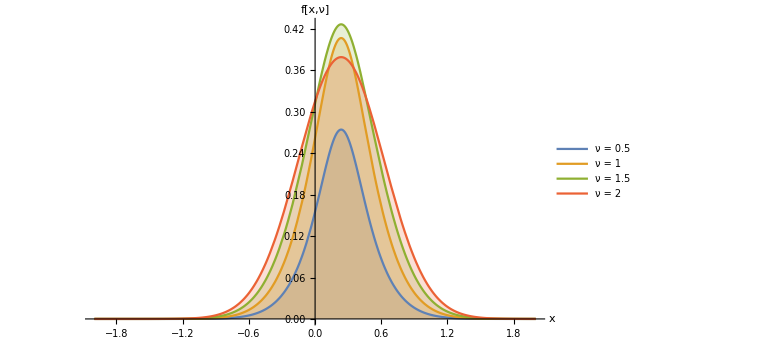

```mathematica
a=Plot[Table[PDF[ChiSquareDistribution[ν],0.9230341547832125-3.1306483061897628 x+6.624164579175652 x^2],{ν,{0.5,1,1.5,2}}]//Evaluate,{x,-2,2},Filling->Axis,AxesLabel->{"x","f[x,ν]"},PlotLegends->{"ν = 0.5","ν = 1","ν = 1.5","ν = 2"},FrameLabel->{{None,None},{None,HoldForm[χ^2]}},PlotLabel->None,LabelStyle->{15,GrayLevel[0],Bold},ImageSize->Large]
```

```mathematica
Export["Ge poly pdf.png",a]
```

Ge poly pdf.png

```mathematica
Mean[ChiSquareDistribution[ν]]
```

ν

```mathematica
Information[ν]
```

```mathematica
TableForm[Table[PDF[ChiSquareDistribution[ν],0.9230341547832125-3.1306483061897628 x+6.624164579175652 x^2],{ν,{0.5,1,1.5,2}}//Evaluate,{x,-2,2}],TableHeadings->{{"ν = 0.5","ν = 1","ν = 1.5","ν = 2"},{"x = 1","x = 2","x = 3","x = 4","x = 5"}}]
```

| x = 1 | x = 2 | x = 3 | x = 4 | x = 5
ν = 0.5 | 8.05543×10^-10 | 0.00018851 | 0.155244 | 0.0083658 | 5.98084×10^-7
ν = 1 | 3.33798×10^-9 | 0.000586142 | 0.261738 | 0.0208606 | 2.20639×10^-6
ν = 1.5 | 9.78056×10^-9 | 0.00128872 | 0.312036 | 0.0367816 | 5.75554×10^-6
ν = 2 | 2.42793×10^-8 | 0.00240052 | 0.315163 | 0.054945 | 0.0000127199

```mathematica
TableForm[Table[CDF[ChiSquareDistribution[ν],0.9230341547832125-3.1306483061897628 x+6.624164579175652 x^2],{ν,{0.5,1,1.5,2}}//Evaluate,{x,-2,2}],TableHeadings->{{"ν = 0.5","ν = 1","ν = 1.5","ν = 2"},{"x = 1","x = 2","x = 3","x = 4","x = 5"}}]
```

| x = 1 | x = 2 | x = 3 | x = 4 | x = 5
ν = 0.5 | 0.9999999984542117 | 0.9996640554424101 | 0.8351123928061663 | 0.9867384951264437 | 0.999998877343033
ν = 1 | 0.9999999935067827 | 0.9989157381896407 | 0.6633204385495759 | 0.9644080795388352 | 0.9999957715527277
ν = 1.5 | 0.9999999807101492 | 0.9975226967335301 | 0.5046131302773945 | 0.9321947820417706 | 0.9999887341199732
ν = 2 | 0.999999951441401 | 0.9951989638514113 | 0.36967333454941687 | 0.8901099780616951 | 0.9999745602571987

```mathematica
Sort[%6]
```

{Piecewise[{{1/2 ⅇ^(1/2 (-0.923034+3.13065 x-6.62416 x^2)), 0.923034-3.13065 x+6.62416 x^2>0}, {0, True}}],Piecewise[{{(0.231932 ⅇ^(1/2 (-0.923034+3.13065 x-6.62416 x^2)))/((0.923034-3.13065 x+6.62416 x^2)^0.75), 0.923034-3.13065 x+6.62416 x^2>0}, {0, True}}],Piecewise[{{(ⅇ^(1/2 (-0.923034+3.13065 x-6.62416 x^2)))/(√(2 π) √(0.923034-3.13065 x+6.62416 x^2)), 0.923034-3.13065 x+6.62416 x^2>0}, {0, True}}],Piecewise[{{(0.485226 ⅇ^(1/2 (-0.923034+3.13065 x-6.62416 x^2)))/((0.923034-3.13065 x+6.62416 x^2)^0.25), 0.923034-3.13065 x+6.62416 x^2>0}, {0, True}}]}

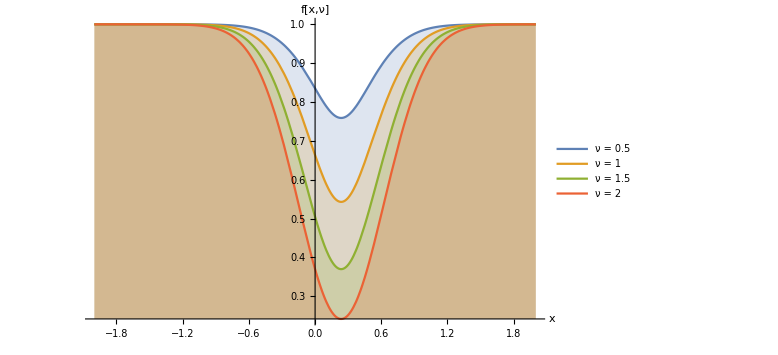

```mathematica
b=Plot[Table[CDF[ChiSquareDistribution[ν],0.9230341547832125-3.1306483061897628 x+6.624164579175652 x^2],{ν,{0.5,1,1.5,2}}]//Evaluate,{x,-2,2},Filling->Axis,AxesLabel->{"x","f[x,ν]"},PlotLegends->{"ν = 0.5","ν = 1","ν = 1.5","ν = 2"},FrameLabel->{{None,None},{None,HoldForm[CDF]}},PlotLabel->None,LabelStyle->{15,GrayLevel[0],Bold},ImageSize->Large]
```

```mathematica
Export["Ge poly cdf.png",b]
```

Ge poly cdf.png

```mathematica
PDF[ChiSquareDistribution[ν],0.9230341547832125-3.1306483061897628 x+6.624164579175652 x^2]
```

Piecewise[{{1/Gamma[ν/2]2^(-ν/2) ⅇ^(1/2 (-0.923034+3.13065 x-6.62416 x^2)) (0.923034-3.13065 x+6.62416 x^2)^(-1+ν/2), 0.923034-3.13065 x+6.62416 x^2>0}, {0, True}}]

```mathematica
Simplify[%10]
```

(2^(1-ν/2) ⅇ^(-21.9398 (0.139343-0.47261 x+1. x^2)^2) (0.923034-3.13065 x+6.62416 x^2)^(-1+ν))/Gamma[ν/2]

```mathematica
ExpandDenominator[(2^(1-ν/2) ⅇ^(-21.93977818600267 (0.13934348154406515-0.4726102844774666 x+1. x^2)^2) (0.9230341547832125-3.1306483061897628 x+6.624164579175652 x^2)^(-1+ν))/Gamma[ν/2]]
```

(2 (0.923034-3.13065 x+6.62416 x^2)^ν)/(0.923034 2^(ν/2) ⅇ^(21.9398 (0.139343-0.47261 x+1. x^2)^2) Gamma[ν/2]-3.13065 2^(ν/2) ⅇ^(21.9398 (0.139343-0.47261 x+1. x^2)^2) x Gamma[ν/2]+6.62416 2^(ν/2) ⅇ^(21.9398 (0.139343-0.47261 x+1. x^2)^2) x^2 Gamma[ν/2])

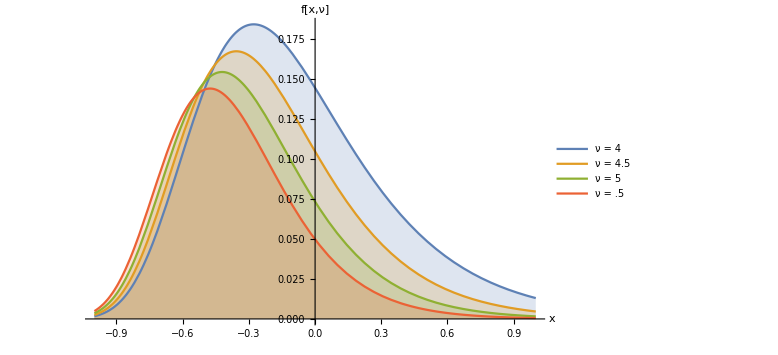

```mathematica
c=Plot[Table[PDF[ChiSquareDistribution[ν],0.9092689759118766 ⅇ^(-2.8332598305453485 t)],{ν,{4,4.5,5,5.5}}]//Evaluate,{t,-1,1},Filling->Axis,AxesLabel->{"x","f[x,ν]"},PlotLegends->{"ν = 4","ν = 4.5","ν = 5","ν = .5"},FrameLabel->{{None,None},{None,HoldForm[CDF]}},PlotLabel->None,LabelStyle->{15,GrayLevel[0],Bold},ImageSize->Large]
```

```mathematica
Export["Ge exp pdf.png",c]
```

Ge exp pdf.png

```mathematica
PDF[ChiSquareDistribution[ν],0.9092689759118766 ⅇ^(-2.8332598305453485 t)]
```

Piecewise[{{(0.909269^(-1+ν/2) 2^(-ν/2) ⅇ^(-0.454634 ⅇ^(-2.83326 t)) (ⅇ^(-2.83326 t))^(-1+ν/2))/Gamma[ν/2], 0.909269 ⅇ^(-2.83326 t)>0}, {0, True}}]

```mathematica
TableForm[Table[PDF[ChiSquareDistribution[ν],0.9092689759118766 ⅇ^(-2.8332598305453485 t)],{ν,{0.5,1,1.5,2}}//Evaluate,{t,-1,1}],TableHeadings->{{"ν = 0.5","ν = 1","ν = 1.5","ν = 2"},{"t = 1","t = 2","t = 3","t = 4","t = 5"}}]
```

| t = 1 | t = 2 | t = 3
ν = 0.5 | 0.0000130847 | 0.158087 | 2.03039
ν = 1 | 0.0000446277 | 0.265533 | 1.67952
ν = 1.5 | 0.000107629 | 0.315374 | 0.982368
ν = 2 | 0.00021991 | 0.31734 | 0.486806

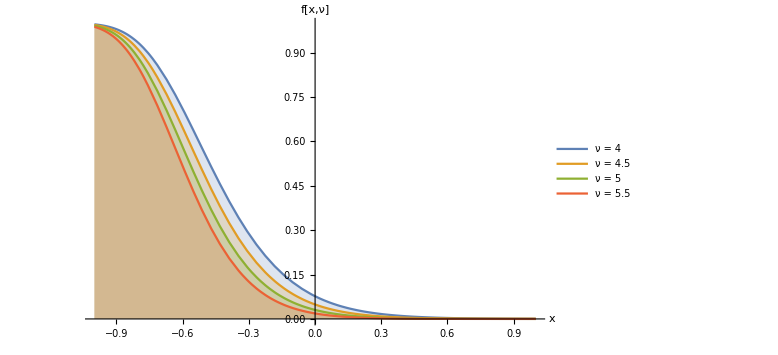

```mathematica
d=Plot[Table[CDF[ChiSquareDistribution[ν],0.9092689759118766 ⅇ^(-2.8332598305453485 t)],{ν,{4,4.5,5,5.5}}]//Evaluate,{t,-1,1},Filling->Axis,AxesLabel->{"x","f[x,ν]"},PlotLegends->{"ν = 4","ν = 4.5","ν = 5","ν = 5.5"},FrameLabel->{{None,None},{None,HoldForm[CDF]}},PlotLabel->None,LabelStyle->{15,GrayLevel[0],Bold},ImageSize->Large]
```

```mathematica
Export["Ge exp cdf.png",d]
```

Ge exp cdf.png

```mathematica
TableForm[Table[CDF[ChiSquareDistribution[ν],0.9092689759118766 ⅇ^(-2.8332598305453485 t)],{ν,{0.5,1,1.5,2}}//Evaluate,{t,-1,1}],TableHeadings->{{"ν = 0.5","ν = 1","ν = 1.5","ν = 2"},{"t = 1","t = 2","t = 3","t = 4","t = 5"}}]
```

| t = 1 | t = 2 | t = 3
ν = 0.5 | 0.999976 | 0.832956 | 0.443778
ν = 1 | 0.999916 | 0.659692 | 0.182892
ν = 1.5 | 0.999791 | 0.500295 | 0.0711355
ν = 2 | 0.99956 | 0.36532 | 0.0263876